1

5

6

30

45

√(x^2+y^2)

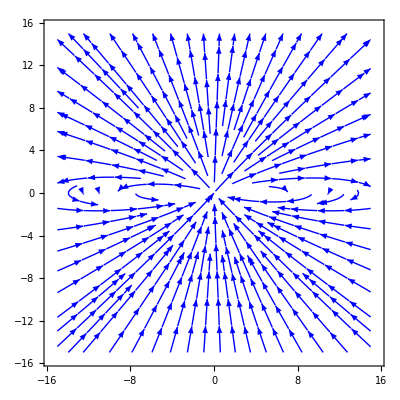

√(x^2+(-6+y)^2)

√(x^2+(6+y)^2)

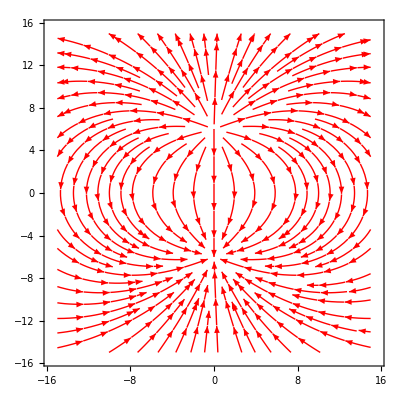

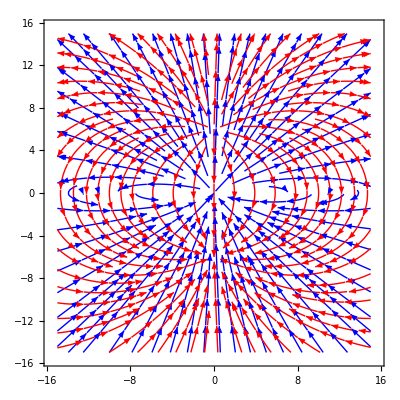

```mathematica
k=1
q=5
d=6
p=q*d
c1=3*k*p/2
r=Sqrt[x^2+y^2]
pure = StreamPlot[{c1*(x*y/(r^5)),c1*((y^2)/(r^5))-1/(r^3)},{x,-15,15},{y,-15,15}, StreamStyle->{Blue}]
part1=Sqrt[x^2+(y-d)^2]
part2=Sqrt[x^2+(y+d)^2]
phys = StreamPlot[{(k*q*(x/(part1^3)-x/(part2^3))),(k*q*((y-d)/(part1^3)-(y+d)/(part2^3)))},{x,-15,15},{y,-15,15}, StreamStyle->{Red}]
Show[pure,phys]
```

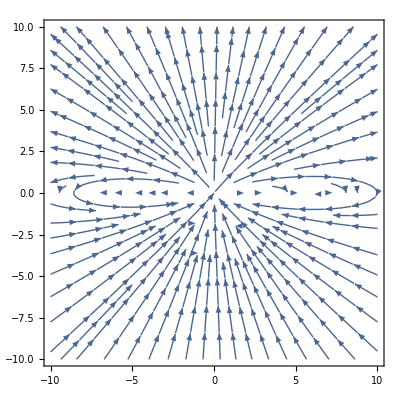

```mathematica
√(x^2+y^2)
```

```mathematica
√(x^2+(-5+y)^2)
```

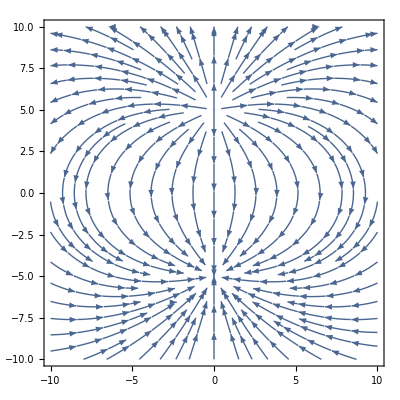

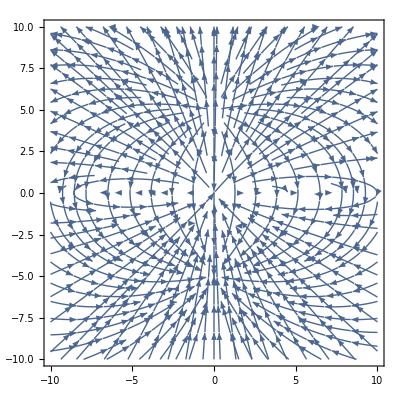

```mathematica
√(x^2+(5+y)^2)
```